```mathematica
?Image
```

Image[data] represents a raster image with pixel values given by the array data.
Image[graphics] creates a raster image from a graphics object. 
Image[obj,options] gives an image that uses the specified options.

```mathematica
Image@
ParallelTable[
x/y,
{x,1,100},
{y,1,100}]
```

-Graphics-

```mathematica
Image@
ParallelTable[
Mod[x,5],
{x,1,100},
{y,1,100}]
```

-Graphics-

```mathematica
Image@
ParallelTable[
EuclideanDistance[{x,y},{50,50}]/EuclideanDistance[{100,100},{50,50}],
{x,1,100},
{y,1,100}]
```

-Graphics-

```mathematica
Image@
ParallelTable[
Mod[EuclideanDistance[{x,y},{50,50}],5]/5,
{x,1,100},
{y,1,100}]
```

-Graphics-

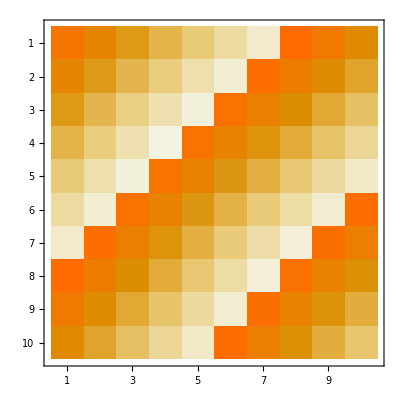

```mathematica
Table[Mod[EuclideanDistance[{x,y},{50,50}],5],{x,1,10},{y,1,10}]//MatrixPlot
```

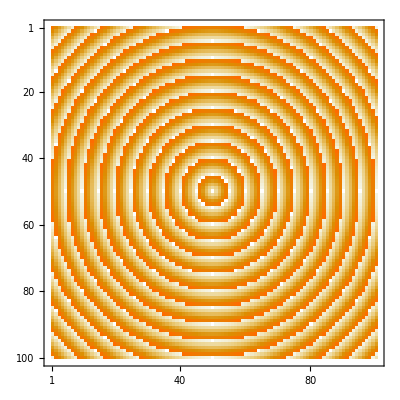

```mathematica
ParallelTable[
Mod[EuclideanDistance[{x,y},{50,50}],5]/EuclideanDistance[{100,100},{50,50}],
{x,1,100},
{y,1,100}]//MatrixPlot
```

```mathematica
Image@
ParallelTable[
Mod[EuclideanDistance[{x,y},{50,50}],5],
{x,1,100},
{y,1,100}]
```

-Graphics-

```mathematica
Image@
ParallelTable[
Block[
{thisDist=EuclideanDistance[{x,y},{50,50}]},
Abs[Mod[thisDist,5]-4]],
{x,1,100},
{y,1,100}]
```

-Graphics-

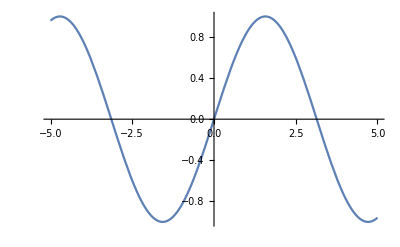

```mathematica
Plot[Sin[x],{x,-5,5}]
```

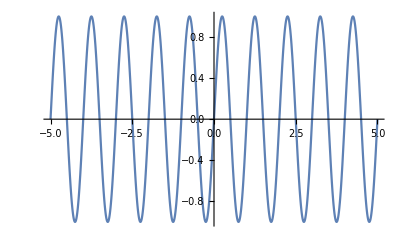

```mathematica
Plot[Sin[x* (2π)/1],{x,-5,5}]
```

```mathematica
Image@
Block[
{phase=10},
ParallelTable[
Block[
{thisDist=EuclideanDistance[{x,y},{50,50}]},
Abs[Mod[thisDist,phase]-phase/2]/(phase/2)],
{x,1,100},
{y,1,100}]]
```

-Graphics-

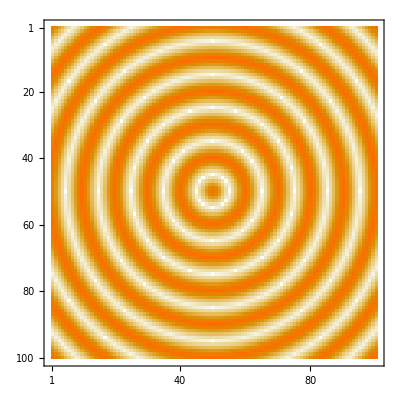

```mathematica
MatrixPlot@
Block[
{phase=10},
ParallelTable[
Block[
{thisDist=EuclideanDistance[{x,y},{50,50}]},
Abs[Mod[thisDist,phase]-phase/2]],
{x,1,100},
{y,1,100}]]
```

```mathematica
?ArcTan
```

ArcTan[z] gives the arc tangent tan^-1(z) of the complex number z. 
ArcTan[x,y] gives the arc tangent of y/x, taking into account which quadrant the point (x,y) is in.

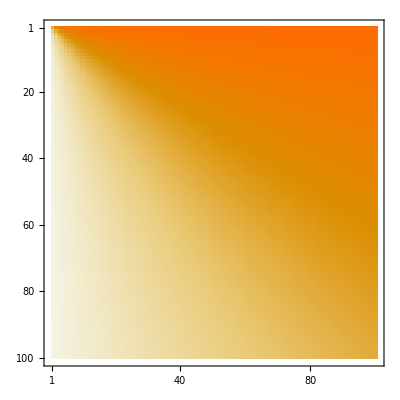

```mathematica
MatrixPlot@
Block[
{phase=10},
ParallelTable[
ArcTan[x,y],
{x,1,100},
{y,1,100}]]
```

ArcTan::indet: Indeterminate expression ArcTan[0, 0] encountered.

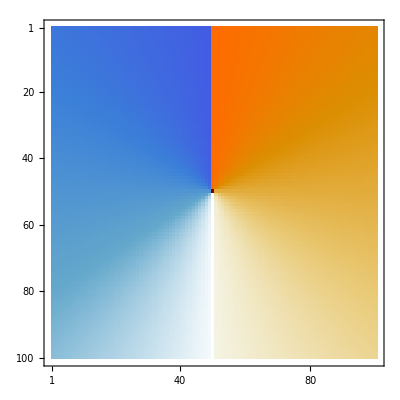

```mathematica
MatrixPlot@
Block[
{phase=10},
ParallelTable[
(ArcTan@@({x,y}-{50,50})),
{x,1,100},
{y,1,100}]]
```

```mathematica
Block[{phase=10},
ParallelTable[
(ArcTan@@({x,y}-{50,50})),
{x,1,100},
{y,1,100}]]//Flatten//Cases[#,_?NumberQ]&
```

ArcTan::indet: Indeterminate expression ArcTan[0, 0] encountered.

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Block[{phase=10},
ParallelTable[
(ArcTan@@({x,y}-{50,50})),
{x,1,100},
{y,1,100}]]//Flatten//N//Cases[#,Except[Indeterminate|∞|-∞]]&//Min
```

ArcTan::indet: Indeterminate expression ArcTan[0, 0] encountered.

-3.12119

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True. 
Select[crit] represents an operator form of Select that can be applied to an expression.

```mathematica
(ArcTan[x,y]+π)/(2π)//FullSimplify
```

(π+ArcTan[x,y])/(2 π)

```mathematica
(ArcTan[0,1]+π)/(2π)//FullSimplify
```

3/4

```mathematica
ArcTan[0,1]
```

π/2

```mathematica
ArcTan[1,1]
```

π/4

```mathematica
ArcTan[1,0]
```

0

```mathematica
ArcTan[-1,0]
```

π

```mathematica
ArcTan[-1,-1]
```

-(3 π)/4

```mathematica
Mod[a,b]/b//FullSimplify
```

Mod[a,b]/b

```mathematica
Block[{b=3},
Table[Mod[a,b]/b,{a,0,10}]]
```

{0,1/3,2/3,0,1/3,2/3,0,1/3,2/3,0,1/3}

```mathematica
sweepLen*markLenNrm==markLen;
```

```mathematica
sweepLen*markLenNrm==markLen
```

```mathematica
markLenNrm==markLen/sweepLen
```

```mathematica
markLenNrm==markLen/sweepLen
```

```mathematica
sinHeight==radPhase*something
```

```mathematica
sinPhase[x_,phase_]:=Sin[(x 2 π)/phase]
```

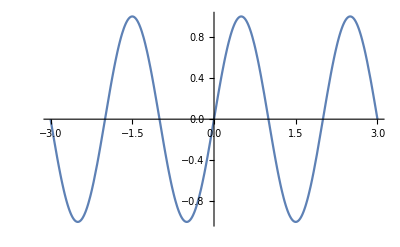

```mathematica
Plot[sinPhase[x,2],{x,-3,3}]
```